```mathematica
H = 1/Sqrt[2]*({{1, 1}, {1, -1}});
iden=({{1, 0}, {0, 1}});
X=({{0, 1}, {1, 0}});
Y=({{0, -I}, {I, 0}});
Z=({{1, 0}, {0, -1}});
S=({{1, 0}, {0, E^(I*Pi/2)}});
PHASE[index_]:=({{1, 0}, {0, E^(I*Pi/2^(index+1))}});

zerozero = ({{1, 0}, {0, 0}});
oneone = ({{0, 0}, {0, 1}});
u[index_]:=  KroneckerProduct[zerozero,PHASE[index]]+KroneckerProduct[oneone,iden];
parser[p_]:=Which[p===0,iden,p===1,X,p===2,Y,p===3,Z];
PauliString[i_,j_]:=KroneckerProduct[parser[i],parser[j]];
pp[index_]:=Sum[KroneckerProduct[u[index],u[index],u[index],u[index]].KroneckerProduct[PauliString[i,j],PauliString[i,j],PauliString[i,j],PauliString[i,j]] -KroneckerProduct[PauliString[i,j],PauliString[i,j],PauliString[i,j],PauliString[i,j]].KroneckerProduct[u[index],u[index],u[index],u[index]] ,{i,0,3},{j,0,3}];
permdouble=Permutations@{{1,2},{3,4},{5,6},{7,8}};

indexToQubitIndices[n_,numQubits_]:=PadLeft[IntegerDigits[n-1,2],numQubits];
permutationMatrix[permutation_]:=With[{numQubits=Length@permutation},SparseArray[{{i_,j_}:>1/;Equal[Permute[indexToQubitIndices[i,numQubits],permutation],indexToQubitIndices[j,numQubits]]},2^numQubits {1,1}]];

oo[index_]:=(1/16)*(1/24)*(pp[index].Sum[permutationMatrix[Flatten[permdouble[[i]]]],{i,1,24}]);

commutator[index_]:= Tr[ConjugateTranspose[oo].oo]
```

```mathematica
kk=Table[{i,
b=oo[i];
Tr[ConjugateTranspose[b].b]},{i,0,10}]
```

{{0,6},{1,9/2},{2,3/4+3/64 (4-4 ⅇ^(-(ⅈ π)/4)) (4-4 ⅇ^((ⅈ π)/4))+3/64 (-4+4 ⅇ^(-(ⅈ π)/4)) (-4+4 ⅇ^((ⅈ π)/4))},{3,3/64 (4-4 ⅇ^(-(ⅈ π)/8)) (4-4 ⅇ^((ⅈ π)/8))+3/64 (-4+4 ⅇ^(-(ⅈ π)/8)) (-4+4 ⅇ^((ⅈ π)/8))+3/256 (4-4 ⅇ^(-(ⅈ π)/4)) (4-4 ⅇ^((ⅈ π)/4))+3/256 (-4+4 ⅇ^(-(ⅈ π)/4)) (-4+4 ⅇ^((ⅈ π)/4))},{4,3/64 (4-4 ⅇ^(-(ⅈ π)/16)) (4-4 ⅇ^((ⅈ π)/16))+3/64 (-4+4 ⅇ^(-(ⅈ π)/16)) (-4+4 ⅇ^((ⅈ π)/16))+3/256 (4-4 ⅇ^(-(ⅈ π)/8)) (4-4 ⅇ^((ⅈ π)/8))+3/256 (-4+4 ⅇ^(-(ⅈ π)/8)) (-4+4 ⅇ^((ⅈ π)/8))},{5,3/64 (4-4 ⅇ^(-(ⅈ π)/32)) (4-4 ⅇ^((ⅈ π)/32))+3/64 (-4+4 ⅇ^(-(ⅈ π)/32)) (-4+4 ⅇ^((ⅈ π)/32))+3/256 (4-4 ⅇ^(-(ⅈ π)/16)) (4-4 ⅇ^((ⅈ π)/16))+3/256 (-4+4 ⅇ^(-(ⅈ π)/16)) (-4+4 ⅇ^((ⅈ π)/16))},{6,3/64 (4-4 ⅇ^(-(ⅈ π)/64)) (4-4 ⅇ^((ⅈ π)/64))+3/64 (-4+4 ⅇ^(-(ⅈ π)/64)) (-4+4 ⅇ^((ⅈ π)/64))+3/256 (4-4 ⅇ^(-(ⅈ π)/32)) (4-4 ⅇ^((ⅈ π)/32))+3/256 (-4+4 ⅇ^(-(ⅈ π)/32)) (-4+4 ⅇ^((ⅈ π)/32))},{7,3/64 (4-4 ⅇ^(-(ⅈ π)/128)) (4-4 ⅇ^((ⅈ π)/128))+3/64 (-4+4 ⅇ^(-(ⅈ π)/128)) (-4+4 ⅇ^((ⅈ π)/128))+3/256 (4-4 ⅇ^(-(ⅈ π)/64)) (4-4 ⅇ^((ⅈ π)/64))+3/256 (-4+4 ⅇ^(-(ⅈ π)/64)) (-4+4 ⅇ^((ⅈ π)/64))},{8,3/64 (4-4 ⅇ^(-(ⅈ π)/256)) (4-4 ⅇ^((ⅈ π)/256))+3/64 (-4+4 ⅇ^(-(ⅈ π)/256)) (-4+4 ⅇ^((ⅈ π)/256))+3/256 (4-4 ⅇ^(-(ⅈ π)/128)) (4-4 ⅇ^((ⅈ π)/128))+3/256 (-4+4 ⅇ^(-(ⅈ π)/128)) (-4+4 ⅇ^((ⅈ π)/128))},{9,3/64 (4-4 ⅇ^(-(ⅈ π)/512)) (4-4 ⅇ^((ⅈ π)/512))+3/64 (-4+4 ⅇ^(-(ⅈ π)/512)) (-4+4 ⅇ^((ⅈ π)/512))+3/256 (4-4 ⅇ^(-(ⅈ π)/256)) (4-4 ⅇ^((ⅈ π)/256))+3/256 (-4+4 ⅇ^(-(ⅈ π)/256)) (-4+4 ⅇ^((ⅈ π)/256))},{10,3/64 (4-4 ⅇ^(-(ⅈ π)/1024)) (4-4 ⅇ^((ⅈ π)/1024))+3/64 (-4+4 ⅇ^(-(ⅈ π)/1024)) (-4+4 ⅇ^((ⅈ π)/1024))+3/256 (4-4 ⅇ^(-(ⅈ π)/512)) (4-4 ⅇ^((ⅈ π)/512))+3/256 (-4+4 ⅇ^(-(ⅈ π)/512)) (-4+4 ⅇ^((ⅈ π)/512))}}

```mathematica
kk//N
```

{{0.,6.},{1.,4.5},{2.,1.62868+0. ⅈ},{3.,0.448031-6.93889×10^-18 ⅈ},{4.,0.114735-8.67362×10^-19 ⅈ},{5.,0.0288569+2.1684×10^-19 ⅈ},{6.,0.00722509+0. ⅈ},{7.,0.00180695-1.69407×10^-21 ⅈ},{8.,0.00045178-4.23516×10^-22 ⅈ},{9.,0.000112948+2.64698×10^-23 ⅈ},{10.,0.0000282371+9.92617×10^-24 ⅈ}}

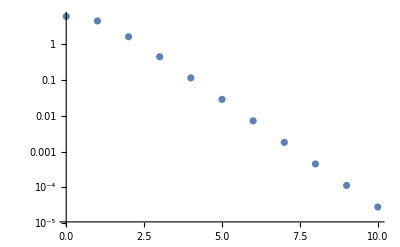

```mathematica
pp1=ListLogPlot[kk]
```

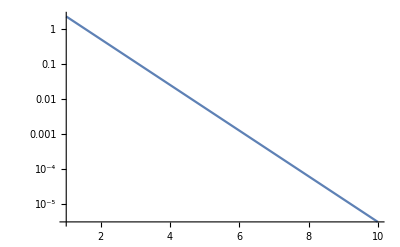

```mathematica
pp2=LogPlot[10*E^(-1.5*x),{x,1,10}]
```

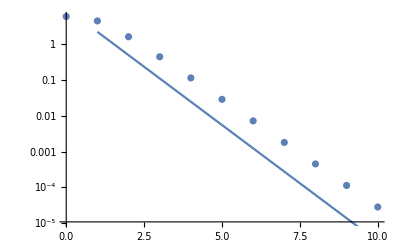

```mathematica
Show[pp1,pp2]
```

```mathematica
Sum[(L-1-j)*E^(-a*j),{j,0,L-1}]
```

(ⅇ^(a-a L) (ⅇ^a-ⅇ^(a+a L)-ⅇ^(a L) L+ⅇ^(a+a L) L))/((-1+ⅇ^a)^2)

```mathematica
FullSimplify[(ⅇ^(a-a L) (ⅇ^a-ⅇ^(a+a L)-ⅇ^(a L) L+ⅇ^(a+a L) L))/((-1+ⅇ^a)^2)]
```

(ⅇ^a (-L+ⅇ^a (-1+ⅇ^(-a L)+L)))/((-1+ⅇ^a)^2)

```mathematica
Limit[%62,L->Infinity]
```

ConditionalExpression[∞,a>0]

```mathematica
Series[%62,{L,Infinity,0}]
```

(ⅇ^(-a L+2 a+O[1/L]^2))/((-1+ⅇ^a)^2)+((ⅇ^a L)/(-1+ⅇ^a)-ⅇ^(2 a)/((-1+ⅇ^a)^2)+O[1/L]^1)

```mathematica
Series[(3*L)/(2^(3*L)),{L,Infinity,1}]
```

ⅇ^(-3 Log[2] L+O[1/L]^2) (3 L+O[1/L]^2)

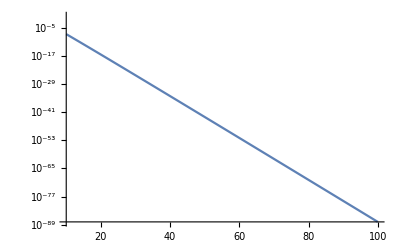

```mathematica
LogPlot[3*L*Exp[-3*Log[2]*L],{L,10,100}]
```

```mathematica
f[L_]:=-Log[1+0.5L];
```

```mathematica
f[7]//N
```

-1.50408

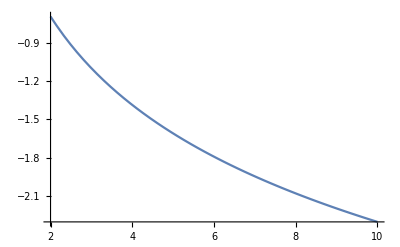

```mathematica
Plot[-Log[L],{L,2,10}]
```

```mathematica
1-E^-0.3
```

0.259182

```mathematica
1.0-E^-3.5
```

0.969803

# 2 qubit commutator for CONTROL+S gate

## Numerical calculation

```mathematica
H = 1/Sqrt[2]*({{1, 1}, {1, -1}});
iden=({{1, 0}, {0, 1}});
X=({{0, 1}, {1, 0}});
Y=({{0, -I}, {I, 0}});
Z=({{1, 0}, {0, -1}});
S=({{1, 0}, {0, E^(I*Pi/2)}});

zerozero = ({{1, 0}, {0, 0}});
oneone = ({{0, 0}, {0, 1}});
u2=KroneckerProduct[zerozero,S]+KroneckerProduct[oneone,iden];
parser[p_]:=Which[p===0,iden,p===1,X,p===2,Y,p===3,Z];
PauliString[i_,j_]:=KroneckerProduct[parser[i],parser[j]];
pp=Sum[KroneckerProduct[u2,u2,u2,u2].KroneckerProduct[PauliString[i,j],PauliString[i,j],PauliString[i,j],PauliString[i,j]] -KroneckerProduct[PauliString[i,j],PauliString[i,j],PauliString[i,j],PauliString[i,j]].KroneckerProduct[u2,u2,u2,u2] ,{i,0,3},{j,0,3}]
```

{1}
 |  |  |  |

```mathematica
Sqrt[Tr[ConjugateTranspose[pp].pp]]
```

48 √2

```mathematica
MatrixPlot[pp,PlotTheme->"Detailed"]
```

-Graphics-

## Analytic - Symbolic Algebra calculation

```mathematica
ClearAll[II,X,Y,Z];
first[A_,B_]:=Which[
(A===II && B===II),TensorProduct[0,II+Z+I*(II-Z)],
(A===II && B===X),TensorProduct[0,(1+I)*X],
(A===II && B===Y),TensorProduct[0,(1+I)*Y],
(A===II && B===Z),TensorProduct[0,II+Z-I*(II-Z)],

(A===X && B===II),TensorProduct[I*Y,II+Z+I*(II-Z)],
(A===X && B===X),TensorProduct[I*Y,(1+I)*X],
(A===X && B===Y),TensorProduct[I*Y,(1+I)*Y],
(A===X && B===Z),TensorProduct[I*Y,II+Z-I*(II-Z)],

(A===Y && B===II),TensorProduct[-I*X,II+Z+I*(II-Z)],
(A===Y && B===X),TensorProduct[-I*X,(1+I)*X],
(A===Y && B===Y),TensorProduct[-I*X,(1+I)*Y],
(A===Y && B===Z),TensorProduct[-I*X,II+Z-I*(II-Z)],

(A===Z && B===II),TensorProduct[0,II+Z+I*(II-Z)],
(A===Z && B===X),TensorProduct[0,(1+I)*X],
(A===Z && B===Y),TensorProduct[0,(1+I)*Y],
(A===Z && B===Z),TensorProduct[0,II+Z-I*(II-Z)]
];

second[A_,B_]:=Which[
(A===II && B===II),TensorProduct[II+Z,0],
(A===II && B===X),TensorProduct[II+Z,(1+I)*Y],
(A===II && B===Y),TensorProduct[II+Z,-(1+I)*X],
(A===II && B===Z),TensorProduct[II+Z,0],

(A===X && B===II),TensorProduct[X,0],
(A===X && B===X),TensorProduct[X,(1+I)*Y],
(A===X && B===Y),TensorProduct[X,-(1+I)*X],
(A===X && B===Z),TensorProduct[X,0],

(A===Y && B===II),TensorProduct[Y,0],
(A===Y && B===X),TensorProduct[Y,(1+I)*Y],
(A===Y && B===Y),TensorProduct[Y,-(1+I)*X],
(A===Y && B===Z),TensorProduct[Y,0],

(A===Z && B===II),TensorProduct[II+Z,0],
(A===Z && B===X),TensorProduct[II+Z,(1+I)*Y],
(A===Z && B===Y),TensorProduct[II+Z,-(1+I)*X],
(A===Z && B===Z),TensorProduct[II+Z,0]
];
third[A_,B_]:=Which[
(A===II && B===II),TensorProduct[0,2*II],
(A===II && B===X),TensorProduct[0,2*X],
(A===II && B===Y),TensorProduct[0,2*Y],
(A===II && B===Z),TensorProduct[0,2*Z],

(A===X && B===II),TensorProduct[-I*Y,2*II],
(A===X && B===X),TensorProduct[-I*Y,2*X],
(A===X && B===Y),TensorProduct[-I*Y,2*Y],
(A===X && B===Z),TensorProduct[-I*Y,2*Z],

(A===Y && B===II),TensorProduct[I*X,2*II],
(A===Y && B===X),TensorProduct[I*X,2*X],
(A===Y && B===Y),TensorProduct[I*X,2*Y],
(A===Y && B===Z),TensorProduct[I*X,2*Z],

(A===Z && B===II),TensorProduct[0,2*II],
(A===Z && B===X),TensorProduct[0,2*X],
(A===Z && B===Y),TensorProduct[0,2*Y],
(A===Z && B===Z),TensorProduct[0,2*Z]
];
fourth[A_,B_]:=Which[
(A===II && B===II),TensorProduct[0,0],
(A===II && B===X),TensorProduct[0,(1+I)*Y],
(A===II && B===Y),TensorProduct[0,-(1+I)*X],
(A===II && B===Z),TensorProduct[0,0],

(A===X && B===II),TensorProduct[I*Y,0],
(A===X && B===X),TensorProduct[I*Y,(1+I)*Y],
(A===X && B===Y),TensorProduct[I*Y,-(1+I)*X],
(A===X && B===Z),TensorProduct[I*Y,0],

(A===Y && B===II),TensorProduct[-I*X,0],
(A===Y && B===X),TensorProduct[-I*X,(1+I)*Y],
(A===Y && B===Y),TensorProduct[-I*X,-(1+I)*X],
(A===Y && B===Z),TensorProduct[-I*X,0],

(A===Z && B===II),TensorProduct[0,0],
(A===Z && B===X),TensorProduct[0,(1+I)*Y],
(A===Z && B===Y),TensorProduct[0,-(1+I)*X],
(A===Z && B===Z),TensorProduct[0,0]
];
fifth[A_,B_]:=Which[
(A===II && B===II),TensorProduct[II+Z,II+Z+I*(II-Z)],
(A===II && B===X),TensorProduct[II+Z,(1+I)*X],
(A===II && B===Y),TensorProduct[II+Z,(1+I)*Y],
(A===II && B===Z),TensorProduct[II+Z,II+Z-I*(II-Z)],

(A===X && B===II),TensorProduct[X,II+Z+I*(II-Z)],
(A===X && B===X),TensorProduct[X,(1+I)*X],
(A===X && B===Y),TensorProduct[X,(1+I)*Y],
(A===X && B===Z),TensorProduct[X,II+Z-I*(II-Z)],

(A===Y && B===II),TensorProduct[Y,II+Z+I*(II-Z)],
(A===Y && B===X),TensorProduct[Y,(1+I)*X],
(A===Y && B===Y),TensorProduct[Y,(1+I)*Y],
(A===Y && B===Z),TensorProduct[Y,II+Z-I*(II-Z)],

(A===Z && B===II),TensorProduct[II+Z,II+Z+I*(II-Z)],
(A===Z && B===X),TensorProduct[II+Z,(1+I)*X],
(A===Z && B===Y),TensorProduct[II+Z,(1+I)*Y],
(A===Z && B===Z),TensorProduct[II+Z,II+Z-I*(II-Z)]
];

sixth[A_,B_]:=Which[
(A===II && B===II),TensorProduct[II-Z,2*II],
(A===II && B===X),TensorProduct[II-Z,2*X],
(A===II && B===Y),TensorProduct[II-Z,2*Y],
(A===II && B===Z),TensorProduct[II-Z,2*Z],

(A===X && B===II),TensorProduct[X,2*II],
(A===X && B===X),TensorProduct[X,2*X],
(A===X && B===Y),TensorProduct[X,2*Y],
(A===X && B===Z),TensorProduct[X,2*Z],

(A===Y && B===II),TensorProduct[Y,2*II],
(A===Y && B===X),TensorProduct[Y,2*X],
(A===Y && B===Y),TensorProduct[Y,2*Y],
(A===Y && B===Z),TensorProduct[Y,2*Z],

(A===Z && B===II),TensorProduct[-(II-Z),2*II],
(A===Z && B===X),TensorProduct[-(II-Z),2*X],
(A===Z && B===Y),TensorProduct[-(II-Z),2*Y],
(A===Z && B===Z),TensorProduct[-(II-Z),2*Z]
];

parser[p_]:=Which[p===1,II,p===2,X,p===3,Y,p===4,Z];

com[i_,j_]:=first[parser[i],parser[j]]+second[parser[i],parser[j]]+third[parser[i],parser[j]];
acom[i_,j_]:=fourth[parser[i],parser[j]]+fifth[parser[i],parser[j]]+sixth[parser[i],parser[j]];
```

```mathematica
kk[II_,X_,Y_,Z_]=(1/128)*Sum[TensorProduct[com[i,j],acom[i,j],acom[i,j],acom[i,j]]+TensorProduct[acom[i,j],com[i,j],acom[i,j],acom[i,j]]+TensorProduct[acom[i,j],acom[i,j],com[i,j],acom[i,j]]+TensorProduct[acom[i,j],acom[i,j],acom[i,j],com[i,j]]+TensorProduct[acom[i,j],com[i,j],com[i,j],com[i,j]]+TensorProduct[com[i,j],acom[i,j],com[i,j],com[i,j]]+TensorProduct[com[i,j],com[i,j],acom[i,j],com[i,j]]+TensorProduct[com[i,j],com[i,j],com[i,j],acom[i,j]],{i,1,4},{j,1,4}];
kk[II,X,Y,Z]//FullSimplify//TensorExpand
```

3/8 ⅈ II⊗X⊗II⊗X⊗II⊗X⊗II⊗Y+3/8 ⅈ II⊗X⊗II⊗X⊗II⊗X⊗Z⊗Y+3/8 ⅈ II⊗X⊗II⊗X⊗II⊗Y⊗II⊗X-1/8 ⅈ II⊗X⊗II⊗X⊗II⊗Y⊗Z⊗X-1/8 ⅈ II⊗X⊗II⊗X⊗Z⊗X⊗II⊗Y-1/8 ⅈ II⊗X⊗II⊗X⊗Z⊗X⊗Z⊗Y+3/8 ⅈ II⊗X⊗II⊗X⊗Z⊗Y⊗II⊗X-1/8 ⅈ II⊗X⊗II⊗X⊗Z⊗Y⊗Z⊗X+3/8 ⅈ II⊗X⊗II⊗Y⊗II⊗X⊗II⊗X-1/8 ⅈ II⊗X⊗II⊗Y⊗II⊗X⊗Z⊗X-3/8 ⅈ II⊗X⊗II⊗Y⊗II⊗Y⊗II⊗Y+1/8 ⅈ II⊗X⊗II⊗Y⊗II⊗Y⊗Z⊗Y-1/8 ⅈ II⊗X⊗II⊗Y⊗Z⊗X⊗II⊗X-1/8 ⅈ II⊗X⊗II⊗Y⊗Z⊗X⊗Z⊗X+1/8 ⅈ II⊗X⊗II⊗Y⊗Z⊗Y⊗II⊗Y+1/8 ⅈ II⊗X⊗II⊗Y⊗Z⊗Y⊗Z⊗Y-1/8 ⅈ II⊗X⊗Z⊗X⊗II⊗X⊗II⊗Y-1/8 ⅈ II⊗X⊗Z⊗X⊗II⊗X⊗Z⊗Y-1/8 ⅈ II⊗X⊗Z⊗X⊗II⊗Y⊗II⊗X-1/8 ⅈ II⊗X⊗Z⊗X⊗II⊗Y⊗Z⊗X-1/8 ⅈ II⊗X⊗Z⊗X⊗Z⊗X⊗II⊗Y-1/8 ⅈ II⊗X⊗Z⊗X⊗Z⊗X⊗Z⊗Y-1/8 ⅈ II⊗X⊗Z⊗X⊗Z⊗Y⊗II⊗X-1/8 ⅈ II⊗X⊗Z⊗X⊗Z⊗Y⊗Z⊗X+3/8 ⅈ II⊗X⊗Z⊗Y⊗II⊗X⊗II⊗X-1/8 ⅈ II⊗X⊗Z⊗Y⊗II⊗X⊗Z⊗X+1/8 ⅈ II⊗X⊗Z⊗Y⊗II⊗Y⊗II⊗Y+1/8 ⅈ II⊗X⊗Z⊗Y⊗II⊗Y⊗Z⊗Y-1/8 ⅈ II⊗X⊗Z⊗Y⊗Z⊗X⊗II⊗X-1/8 ⅈ II⊗X⊗Z⊗Y⊗Z⊗X⊗Z⊗X+1/8 ⅈ II⊗X⊗Z⊗Y⊗Z⊗Y⊗II⊗Y-3/8 ⅈ II⊗X⊗Z⊗Y⊗Z⊗Y⊗Z⊗Y+3/8 ⅈ II⊗Y⊗II⊗X⊗II⊗X⊗II⊗X-1/8 ⅈ II⊗Y⊗II⊗X⊗II⊗X⊗Z⊗X-3/8 ⅈ II⊗Y⊗II⊗X⊗II⊗Y⊗II⊗Y+1/8 ⅈ II⊗Y⊗II⊗X⊗II⊗Y⊗Z⊗Y-1/8 ⅈ II⊗Y⊗II⊗X⊗Z⊗X⊗II⊗X-1/8 ⅈ II⊗Y⊗II⊗X⊗Z⊗X⊗Z⊗X+1/8 ⅈ II⊗Y⊗II⊗X⊗Z⊗Y⊗II⊗Y+1/8 ⅈ II⊗Y⊗II⊗X⊗Z⊗Y⊗Z⊗Y-3/8 ⅈ II⊗Y⊗II⊗Y⊗II⊗X⊗II⊗Y+1/8 ⅈ II⊗Y⊗II⊗Y⊗II⊗X⊗Z⊗Y-3/8 ⅈ II⊗Y⊗II⊗Y⊗II⊗Y⊗II⊗X-3/8 ⅈ II⊗Y⊗II⊗Y⊗II⊗Y⊗Z⊗X-3/8 ⅈ II⊗Y⊗II⊗Y⊗Z⊗X⊗II⊗Y+1/8 ⅈ II⊗Y⊗II⊗Y⊗Z⊗X⊗Z⊗Y+1/8 ⅈ II⊗Y⊗II⊗Y⊗Z⊗Y⊗II⊗X+1/8 ⅈ II⊗Y⊗II⊗Y⊗Z⊗Y⊗Z⊗X-1/8 ⅈ II⊗Y⊗Z⊗X⊗II⊗X⊗II⊗X-1/8 ⅈ II⊗Y⊗Z⊗X⊗II⊗X⊗Z⊗X-3/8 ⅈ II⊗Y⊗Z⊗X⊗II⊗Y⊗II⊗Y+1/8 ⅈ II⊗Y⊗Z⊗X⊗II⊗Y⊗Z⊗Y-1/8 ⅈ II⊗Y⊗Z⊗X⊗Z⊗X⊗II⊗X+3/8 ⅈ II⊗Y⊗Z⊗X⊗Z⊗X⊗Z⊗X+1/8 ⅈ II⊗Y⊗Z⊗X⊗Z⊗Y⊗II⊗Y+1/8 ⅈ II⊗Y⊗Z⊗X⊗Z⊗Y⊗Z⊗Y+1/8 ⅈ II⊗Y⊗Z⊗Y⊗II⊗X⊗II⊗Y+1/8 ⅈ II⊗Y⊗Z⊗Y⊗II⊗X⊗Z⊗Y+1/8 ⅈ II⊗Y⊗Z⊗Y⊗II⊗Y⊗II⊗X+1/8 ⅈ II⊗Y⊗Z⊗Y⊗II⊗Y⊗Z⊗X+1/8 ⅈ II⊗Y⊗Z⊗Y⊗Z⊗X⊗II⊗Y+1/8 ⅈ II⊗Y⊗Z⊗Y⊗Z⊗X⊗Z⊗Y+1/8 ⅈ II⊗Y⊗Z⊗Y⊗Z⊗Y⊗II⊗X+1/8 ⅈ II⊗Y⊗Z⊗Y⊗Z⊗Y⊗Z⊗X-3/8 ⅈ X⊗II⊗X⊗II⊗X⊗II⊗Y⊗II+3/8 ⅈ X⊗II⊗X⊗II⊗X⊗II⊗Y⊗Z-1/8 ⅈ X⊗II⊗X⊗II⊗X⊗Z⊗Y⊗II+1/8 ⅈ X⊗II⊗X⊗II⊗X⊗Z⊗Y⊗Z-3/8 ⅈ X⊗II⊗X⊗II⊗Y⊗II⊗X⊗II-1/8 ⅈ X⊗II⊗X⊗II⊗Y⊗II⊗X⊗Z+3/8 ⅈ X⊗II⊗X⊗II⊗Y⊗Z⊗X⊗II+1/8 ⅈ X⊗II⊗X⊗II⊗Y⊗Z⊗X⊗Z-1/8 ⅈ X⊗II⊗X⊗Z⊗X⊗II⊗Y⊗II+1/8 ⅈ X⊗II⊗X⊗Z⊗X⊗II⊗Y⊗Z+1/8 ⅈ X⊗II⊗X⊗Z⊗X⊗Z⊗Y⊗II-1/8 ⅈ X⊗II⊗X⊗Z⊗X⊗Z⊗Y⊗Z-1/8 ⅈ X⊗II⊗X⊗Z⊗Y⊗II⊗X⊗II+1/8 ⅈ X⊗II⊗X⊗Z⊗Y⊗II⊗X⊗Z+1/8 ⅈ X⊗II⊗X⊗Z⊗Y⊗Z⊗X⊗II-1/8 ⅈ X⊗II⊗X⊗Z⊗Y⊗Z⊗X⊗Z-3/8 ⅈ X⊗II⊗Y⊗II⊗X⊗II⊗X⊗II-1/8 ⅈ X⊗II⊗Y⊗II⊗X⊗II⊗X⊗Z-1/8 ⅈ X⊗II⊗Y⊗II⊗X⊗Z⊗X⊗II+1/8 ⅈ X⊗II⊗Y⊗II⊗X⊗Z⊗X⊗Z+3/8 ⅈ X⊗II⊗Y⊗II⊗Y⊗II⊗Y⊗II+1/8 ⅈ X⊗II⊗Y⊗II⊗Y⊗II⊗Y⊗Z+1/8 ⅈ X⊗II⊗Y⊗II⊗Y⊗Z⊗Y⊗II-1/8 ⅈ X⊗II⊗Y⊗II⊗Y⊗Z⊗Y⊗Z+3/8 ⅈ X⊗II⊗Y⊗Z⊗X⊗II⊗X⊗II+1/8 ⅈ X⊗II⊗Y⊗Z⊗X⊗II⊗X⊗Z+1/8 ⅈ X⊗II⊗Y⊗Z⊗X⊗Z⊗X⊗II-1/8 ⅈ X⊗II⊗Y⊗Z⊗X⊗Z⊗X⊗Z+1/8 ⅈ X⊗II⊗Y⊗Z⊗Y⊗II⊗Y⊗II-1/8 ⅈ X⊗II⊗Y⊗Z⊗Y⊗II⊗Y⊗Z-1/8 ⅈ X⊗II⊗Y⊗Z⊗Y⊗Z⊗Y⊗II-3/8 ⅈ X⊗II⊗Y⊗Z⊗Y⊗Z⊗Y⊗Z+3/8 ⅈ X⊗X⊗X⊗X⊗X⊗X⊗X⊗Y-3/8 ⅈ X⊗X⊗X⊗X⊗X⊗X⊗Y⊗X+3/8 ⅈ X⊗X⊗X⊗X⊗X⊗Y⊗X⊗X-1/8 ⅈ X⊗X⊗X⊗X⊗X⊗Y⊗Y⊗Y-3/8 ⅈ X⊗X⊗X⊗X⊗Y⊗X⊗X⊗X+1/8 ⅈ X⊗X⊗X⊗X⊗Y⊗X⊗Y⊗Y-1/8 ⅈ X⊗X⊗X⊗X⊗Y⊗Y⊗X⊗Y+1/8 ⅈ X⊗X⊗X⊗X⊗Y⊗Y⊗Y⊗X+3/8 ⅈ X⊗X⊗X⊗Y⊗X⊗X⊗X⊗X-1/8 ⅈ X⊗X⊗X⊗Y⊗X⊗X⊗Y⊗Y-3/8 ⅈ X⊗X⊗X⊗Y⊗X⊗Y⊗X⊗Y-1/8 ⅈ X⊗X⊗X⊗Y⊗X⊗Y⊗Y⊗X-1/8 ⅈ X⊗X⊗X⊗Y⊗Y⊗X⊗X⊗Y+1/8 ⅈ X⊗X⊗X⊗Y⊗Y⊗X⊗Y⊗X-1/8 ⅈ X⊗X⊗X⊗Y⊗Y⊗Y⊗X⊗X-1/8 ⅈ X⊗X⊗X⊗Y⊗Y⊗Y⊗Y⊗Y-3/8 ⅈ X⊗X⊗Y⊗X⊗X⊗X⊗X⊗X+1/8 ⅈ X⊗X⊗Y⊗X⊗X⊗X⊗Y⊗Y-1/8 ⅈ X⊗X⊗Y⊗X⊗X⊗Y⊗X⊗Y+1/8 ⅈ X⊗X⊗Y⊗X⊗X⊗Y⊗Y⊗X+1/8 ⅈ X⊗X⊗Y⊗X⊗Y⊗X⊗X⊗Y+3/8 ⅈ X⊗X⊗Y⊗X⊗Y⊗X⊗Y⊗X+1/8 ⅈ X⊗X⊗Y⊗X⊗Y⊗Y⊗X⊗X+1/8 ⅈ X⊗X⊗Y⊗X⊗Y⊗Y⊗Y⊗Y-1/8 ⅈ X⊗X⊗Y⊗Y⊗X⊗X⊗X⊗Y+1/8 ⅈ X⊗X⊗Y⊗Y⊗X⊗X⊗Y⊗X-1/8 ⅈ X⊗X⊗Y⊗Y⊗X⊗Y⊗X⊗X-1/8 ⅈ X⊗X⊗Y⊗Y⊗X⊗Y⊗Y⊗Y+1/8 ⅈ X⊗X⊗Y⊗Y⊗Y⊗X⊗X⊗X+1/8 ⅈ X⊗X⊗Y⊗Y⊗Y⊗X⊗Y⊗Y-1/8 ⅈ X⊗X⊗Y⊗Y⊗Y⊗Y⊗X⊗Y+1/8 ⅈ X⊗X⊗Y⊗Y⊗Y⊗Y⊗Y⊗X+3/8 ⅈ X⊗Y⊗X⊗X⊗X⊗X⊗X⊗X-1/8 ⅈ X⊗Y⊗X⊗X⊗X⊗X⊗Y⊗Y-3/8 ⅈ X⊗Y⊗X⊗X⊗X⊗Y⊗X⊗Y-1/8 ⅈ X⊗Y⊗X⊗X⊗X⊗Y⊗Y⊗X-1/8 ⅈ X⊗Y⊗X⊗X⊗Y⊗X⊗X⊗Y+1/8 ⅈ X⊗Y⊗X⊗X⊗Y⊗X⊗Y⊗X-1/8 ⅈ X⊗Y⊗X⊗X⊗Y⊗Y⊗X⊗X-1/8 ⅈ X⊗Y⊗X⊗X⊗Y⊗Y⊗Y⊗Y-3/8 ⅈ X⊗Y⊗X⊗Y⊗X⊗X⊗X⊗Y-1/8 ⅈ X⊗Y⊗X⊗Y⊗X⊗X⊗Y⊗X-3/8 ⅈ X⊗Y⊗X⊗Y⊗X⊗Y⊗X⊗X-3/8 ⅈ X⊗Y⊗X⊗Y⊗X⊗Y⊗Y⊗Y-1/8 ⅈ X⊗Y⊗X⊗Y⊗Y⊗X⊗X⊗X-1/8 ⅈ X⊗Y⊗X⊗Y⊗Y⊗X⊗Y⊗Y-3/8 ⅈ X⊗Y⊗X⊗Y⊗Y⊗Y⊗X⊗Y-1/8 ⅈ X⊗Y⊗X⊗Y⊗Y⊗Y⊗Y⊗X-1/8 ⅈ X⊗Y⊗Y⊗X⊗X⊗X⊗X⊗Y+1/8 ⅈ X⊗Y⊗Y⊗X⊗X⊗X⊗Y⊗X-1/8 ⅈ X⊗Y⊗Y⊗X⊗X⊗Y⊗X⊗X-1/8 ⅈ X⊗Y⊗Y⊗X⊗X⊗Y⊗Y⊗Y+1/8 ⅈ X⊗Y⊗Y⊗X⊗Y⊗X⊗X⊗X+1/8 ⅈ X⊗Y⊗Y⊗X⊗Y⊗X⊗Y⊗Y-1/8 ⅈ X⊗Y⊗Y⊗X⊗Y⊗Y⊗X⊗Y+1/8 ⅈ X⊗Y⊗Y⊗X⊗Y⊗Y⊗Y⊗X-1/8 ⅈ X⊗Y⊗Y⊗Y⊗X⊗X⊗X⊗X-1/8 ⅈ X⊗Y⊗Y⊗Y⊗X⊗X⊗Y⊗Y-3/8 ⅈ X⊗Y⊗Y⊗Y⊗X⊗Y⊗X⊗Y-1/8 ⅈ X⊗Y⊗Y⊗Y⊗X⊗Y⊗Y⊗X-1/8 ⅈ X⊗Y⊗Y⊗Y⊗Y⊗X⊗X⊗Y+1/8 ⅈ X⊗Y⊗Y⊗Y⊗Y⊗X⊗Y⊗X-1/8 ⅈ X⊗Y⊗Y⊗Y⊗Y⊗Y⊗X⊗X+3/8 ⅈ X⊗Y⊗Y⊗Y⊗Y⊗Y⊗Y⊗Y-1/8 ⅈ X⊗Z⊗X⊗II⊗X⊗II⊗Y⊗II+1/8 ⅈ X⊗Z⊗X⊗II⊗X⊗II⊗Y⊗Z+1/8 ⅈ X⊗Z⊗X⊗II⊗X⊗Z⊗Y⊗II-1/8 ⅈ X⊗Z⊗X⊗II⊗X⊗Z⊗Y⊗Z-1/8 ⅈ X⊗Z⊗X⊗II⊗Y⊗II⊗X⊗II+1/8 ⅈ X⊗Z⊗X⊗II⊗Y⊗II⊗X⊗Z+1/8 ⅈ X⊗Z⊗X⊗II⊗Y⊗Z⊗X⊗II-1/8 ⅈ X⊗Z⊗X⊗II⊗Y⊗Z⊗X⊗Z+1/8 ⅈ X⊗Z⊗X⊗Z⊗X⊗II⊗Y⊗II-1/8 ⅈ X⊗Z⊗X⊗Z⊗X⊗II⊗Y⊗Z+3/8 ⅈ X⊗Z⊗X⊗Z⊗X⊗Z⊗Y⊗II-3/8 ⅈ X⊗Z⊗X⊗Z⊗X⊗Z⊗Y⊗Z+1/8 ⅈ X⊗Z⊗X⊗Z⊗Y⊗II⊗X⊗II+3/8 ⅈ X⊗Z⊗X⊗Z⊗Y⊗II⊗X⊗Z-1/8 ⅈ X⊗Z⊗X⊗Z⊗Y⊗Z⊗X⊗II-3/8 ⅈ X⊗Z⊗X⊗Z⊗Y⊗Z⊗X⊗Z-1/8 ⅈ X⊗Z⊗Y⊗II⊗X⊗II⊗X⊗II+1/8 ⅈ X⊗Z⊗Y⊗II⊗X⊗II⊗X⊗Z+1/8 ⅈ X⊗Z⊗Y⊗II⊗X⊗Z⊗X⊗II+3/8 ⅈ X⊗Z⊗Y⊗II⊗X⊗Z⊗X⊗Z-3/8 ⅈ X⊗Z⊗Y⊗II⊗Y⊗II⊗Y⊗II-1/8 ⅈ X⊗Z⊗Y⊗II⊗Y⊗II⊗Y⊗Z-1/8 ⅈ X⊗Z⊗Y⊗II⊗Y⊗Z⊗Y⊗II+1/8 ⅈ X⊗Z⊗Y⊗II⊗Y⊗Z⊗Y⊗Z+1/8 ⅈ X⊗Z⊗Y⊗Z⊗X⊗II⊗X⊗II-1/8 ⅈ X⊗Z⊗Y⊗Z⊗X⊗II⊗X⊗Z-1/8 ⅈ X⊗Z⊗Y⊗Z⊗X⊗Z⊗X⊗II-3/8 ⅈ X⊗Z⊗Y⊗Z⊗X⊗Z⊗X⊗Z-1/8 ⅈ X⊗Z⊗Y⊗Z⊗Y⊗II⊗Y⊗II+1/8 ⅈ X⊗Z⊗Y⊗Z⊗Y⊗II⊗Y⊗Z+1/8 ⅈ X⊗Z⊗Y⊗Z⊗Y⊗Z⊗Y⊗II+3/8 ⅈ X⊗Z⊗Y⊗Z⊗Y⊗Z⊗Y⊗Z-3/8 ⅈ Y⊗II⊗X⊗II⊗X⊗II⊗X⊗II-1/8 ⅈ Y⊗II⊗X⊗II⊗X⊗II⊗X⊗Z-1/8 ⅈ Y⊗II⊗X⊗II⊗X⊗Z⊗X⊗II+1/8 ⅈ Y⊗II⊗X⊗II⊗X⊗Z⊗X⊗Z+3/8 ⅈ Y⊗II⊗X⊗II⊗Y⊗II⊗Y⊗II+1/8 ⅈ Y⊗II⊗X⊗II⊗Y⊗II⊗Y⊗Z+1/8 ⅈ Y⊗II⊗X⊗II⊗Y⊗Z⊗Y⊗II-1/8 ⅈ Y⊗II⊗X⊗II⊗Y⊗Z⊗Y⊗Z-1/8 ⅈ Y⊗II⊗X⊗Z⊗X⊗II⊗X⊗II+1/8 ⅈ Y⊗II⊗X⊗Z⊗X⊗II⊗X⊗Z+1/8 ⅈ Y⊗II⊗X⊗Z⊗X⊗Z⊗X⊗II+3/8 ⅈ Y⊗II⊗X⊗Z⊗X⊗Z⊗X⊗Z-3/8 ⅈ Y⊗II⊗X⊗Z⊗Y⊗II⊗Y⊗II-1/8 ⅈ Y⊗II⊗X⊗Z⊗Y⊗II⊗Y⊗Z-1/8 ⅈ Y⊗II⊗X⊗Z⊗Y⊗Z⊗Y⊗II+1/8 ⅈ Y⊗II⊗X⊗Z⊗Y⊗Z⊗Y⊗Z+3/8 ⅈ Y⊗II⊗Y⊗II⊗X⊗II⊗Y⊗II+1/8 ⅈ Y⊗II⊗Y⊗II⊗X⊗II⊗Y⊗Z-3/8 ⅈ Y⊗II⊗Y⊗II⊗X⊗Z⊗Y⊗II-1/8 ⅈ Y⊗II⊗Y⊗II⊗X⊗Z⊗Y⊗Z+3/8 ⅈ Y⊗II⊗Y⊗II⊗Y⊗II⊗X⊗II-3/8 ⅈ Y⊗II⊗Y⊗II⊗Y⊗II⊗X⊗Z+1/8 ⅈ Y⊗II⊗Y⊗II⊗Y⊗Z⊗X⊗II-1/8 ⅈ Y⊗II⊗Y⊗II⊗Y⊗Z⊗X⊗Z+1/8 ⅈ Y⊗II⊗Y⊗Z⊗X⊗II⊗Y⊗II-1/8 ⅈ Y⊗II⊗Y⊗Z⊗X⊗II⊗Y⊗Z-1/8 ⅈ Y⊗II⊗Y⊗Z⊗X⊗Z⊗Y⊗II+1/8 ⅈ Y⊗II⊗Y⊗Z⊗X⊗Z⊗Y⊗Z+1/8 ⅈ Y⊗II⊗Y⊗Z⊗Y⊗II⊗X⊗II-1/8 ⅈ Y⊗II⊗Y⊗Z⊗Y⊗II⊗X⊗Z-1/8 ⅈ Y⊗II⊗Y⊗Z⊗Y⊗Z⊗X⊗II+1/8 ⅈ Y⊗II⊗Y⊗Z⊗Y⊗Z⊗X⊗Z-3/8 ⅈ Y⊗X⊗X⊗X⊗X⊗X⊗X⊗X+1/8 ⅈ Y⊗X⊗X⊗X⊗X⊗X⊗Y⊗Y-1/8 ⅈ Y⊗X⊗X⊗X⊗X⊗Y⊗X⊗Y+1/8 ⅈ Y⊗X⊗X⊗X⊗X⊗Y⊗Y⊗X+1/8 ⅈ Y⊗X⊗X⊗X⊗Y⊗X⊗X⊗Y+3/8 ⅈ Y⊗X⊗X⊗X⊗Y⊗X⊗Y⊗X+1/8 ⅈ Y⊗X⊗X⊗X⊗Y⊗Y⊗X⊗X+1/8 ⅈ Y⊗X⊗X⊗X⊗Y⊗Y⊗Y⊗Y-1/8 ⅈ Y⊗X⊗X⊗Y⊗X⊗X⊗X⊗Y+1/8 ⅈ Y⊗X⊗X⊗Y⊗X⊗X⊗Y⊗X-1/8 ⅈ Y⊗X⊗X⊗Y⊗X⊗Y⊗X⊗X-1/8 ⅈ Y⊗X⊗X⊗Y⊗X⊗Y⊗Y⊗Y+1/8 ⅈ Y⊗X⊗X⊗Y⊗Y⊗X⊗X⊗X+1/8 ⅈ Y⊗X⊗X⊗Y⊗Y⊗X⊗Y⊗Y-1/8 ⅈ Y⊗X⊗X⊗Y⊗Y⊗Y⊗X⊗Y+1/8 ⅈ Y⊗X⊗X⊗Y⊗Y⊗Y⊗Y⊗X+1/8 ⅈ Y⊗X⊗Y⊗X⊗X⊗X⊗X⊗Y+3/8 ⅈ Y⊗X⊗Y⊗X⊗X⊗X⊗Y⊗X+1/8 ⅈ Y⊗X⊗Y⊗X⊗X⊗Y⊗X⊗X+1/8 ⅈ Y⊗X⊗Y⊗X⊗X⊗Y⊗Y⊗Y+3/8 ⅈ Y⊗X⊗Y⊗X⊗Y⊗X⊗X⊗X+3/8 ⅈ Y⊗X⊗Y⊗X⊗Y⊗X⊗Y⊗Y+1/8 ⅈ Y⊗X⊗Y⊗X⊗Y⊗Y⊗X⊗Y+3/8 ⅈ Y⊗X⊗Y⊗X⊗Y⊗Y⊗Y⊗X+1/8 ⅈ Y⊗X⊗Y⊗Y⊗X⊗X⊗X⊗X+1/8 ⅈ Y⊗X⊗Y⊗Y⊗X⊗X⊗Y⊗Y-1/8 ⅈ Y⊗X⊗Y⊗Y⊗X⊗Y⊗X⊗Y+1/8 ⅈ Y⊗X⊗Y⊗Y⊗X⊗Y⊗Y⊗X+1/8 ⅈ Y⊗X⊗Y⊗Y⊗Y⊗X⊗X⊗Y+3/8 ⅈ Y⊗X⊗Y⊗Y⊗Y⊗X⊗Y⊗X+1/8 ⅈ Y⊗X⊗Y⊗Y⊗Y⊗Y⊗X⊗X-3/8 ⅈ Y⊗X⊗Y⊗Y⊗Y⊗Y⊗Y⊗Y-1/8 ⅈ Y⊗Y⊗X⊗X⊗X⊗X⊗X⊗Y+1/8 ⅈ Y⊗Y⊗X⊗X⊗X⊗X⊗Y⊗X-1/8 ⅈ Y⊗Y⊗X⊗X⊗X⊗Y⊗X⊗X-1/8 ⅈ Y⊗Y⊗X⊗X⊗X⊗Y⊗Y⊗Y+1/8 ⅈ Y⊗Y⊗X⊗X⊗Y⊗X⊗X⊗X+1/8 ⅈ Y⊗Y⊗X⊗X⊗Y⊗X⊗Y⊗Y-1/8 ⅈ Y⊗Y⊗X⊗X⊗Y⊗Y⊗X⊗Y+1/8 ⅈ Y⊗Y⊗X⊗X⊗Y⊗Y⊗Y⊗X-1/8 ⅈ Y⊗Y⊗X⊗Y⊗X⊗X⊗X⊗X-1/8 ⅈ Y⊗Y⊗X⊗Y⊗X⊗X⊗Y⊗Y-3/8 ⅈ Y⊗Y⊗X⊗Y⊗X⊗Y⊗X⊗Y-1/8 ⅈ Y⊗Y⊗X⊗Y⊗X⊗Y⊗Y⊗X-1/8 ⅈ Y⊗Y⊗X⊗Y⊗Y⊗X⊗X⊗Y+1/8 ⅈ Y⊗Y⊗X⊗Y⊗Y⊗X⊗Y⊗X-1/8 ⅈ Y⊗Y⊗X⊗Y⊗Y⊗Y⊗X⊗X+3/8 ⅈ Y⊗Y⊗X⊗Y⊗Y⊗Y⊗Y⊗Y+1/8 ⅈ Y⊗Y⊗Y⊗X⊗X⊗X⊗X⊗X+1/8 ⅈ Y⊗Y⊗Y⊗X⊗X⊗X⊗Y⊗Y-1/8 ⅈ Y⊗Y⊗Y⊗X⊗X⊗Y⊗X⊗Y+1/8 ⅈ Y⊗Y⊗Y⊗X⊗X⊗Y⊗Y⊗X+1/8 ⅈ Y⊗Y⊗Y⊗X⊗Y⊗X⊗X⊗Y+3/8 ⅈ Y⊗Y⊗Y⊗X⊗Y⊗X⊗Y⊗X+1/8 ⅈ Y⊗Y⊗Y⊗X⊗Y⊗Y⊗X⊗X-3/8 ⅈ Y⊗Y⊗Y⊗X⊗Y⊗Y⊗Y⊗Y-1/8 ⅈ Y⊗Y⊗Y⊗Y⊗X⊗X⊗X⊗Y+1/8 ⅈ Y⊗Y⊗Y⊗Y⊗X⊗X⊗Y⊗X-1/8 ⅈ Y⊗Y⊗Y⊗Y⊗X⊗Y⊗X⊗X+3/8 ⅈ Y⊗Y⊗Y⊗Y⊗X⊗Y⊗Y⊗Y+1/8 ⅈ Y⊗Y⊗Y⊗Y⊗Y⊗X⊗X⊗X-3/8 ⅈ Y⊗Y⊗Y⊗Y⊗Y⊗X⊗Y⊗Y+3/8 ⅈ Y⊗Y⊗Y⊗Y⊗Y⊗Y⊗X⊗Y-3/8 ⅈ Y⊗Y⊗Y⊗Y⊗Y⊗Y⊗Y⊗X+3/8 ⅈ Y⊗Z⊗X⊗II⊗X⊗II⊗X⊗II+1/8 ⅈ Y⊗Z⊗X⊗II⊗X⊗II⊗X⊗Z+1/8 ⅈ Y⊗Z⊗X⊗II⊗X⊗Z⊗X⊗II-1/8 ⅈ Y⊗Z⊗X⊗II⊗X⊗Z⊗X⊗Z+1/8 ⅈ Y⊗Z⊗X⊗II⊗Y⊗II⊗Y⊗II-1/8 ⅈ Y⊗Z⊗X⊗II⊗Y⊗II⊗Y⊗Z-1/8 ⅈ Y⊗Z⊗X⊗II⊗Y⊗Z⊗Y⊗II-3/8 ⅈ Y⊗Z⊗X⊗II⊗Y⊗Z⊗Y⊗Z+1/8 ⅈ Y⊗Z⊗X⊗Z⊗X⊗II⊗X⊗II-1/8 ⅈ Y⊗Z⊗X⊗Z⊗X⊗II⊗X⊗Z-1/8 ⅈ Y⊗Z⊗X⊗Z⊗X⊗Z⊗X⊗II-3/8 ⅈ Y⊗Z⊗X⊗Z⊗X⊗Z⊗X⊗Z-1/8 ⅈ Y⊗Z⊗X⊗Z⊗Y⊗II⊗Y⊗II+1/8 ⅈ Y⊗Z⊗X⊗Z⊗Y⊗II⊗Y⊗Z+1/8 ⅈ Y⊗Z⊗X⊗Z⊗Y⊗Z⊗Y⊗II+3/8 ⅈ Y⊗Z⊗X⊗Z⊗Y⊗Z⊗Y⊗Z+1/8 ⅈ Y⊗Z⊗Y⊗II⊗X⊗II⊗Y⊗II-1/8 ⅈ Y⊗Z⊗Y⊗II⊗X⊗II⊗Y⊗Z-1/8 ⅈ Y⊗Z⊗Y⊗II⊗X⊗Z⊗Y⊗II+1/8 ⅈ Y⊗Z⊗Y⊗II⊗X⊗Z⊗Y⊗Z+1/8 ⅈ Y⊗Z⊗Y⊗II⊗Y⊗II⊗X⊗II-1/8 ⅈ Y⊗Z⊗Y⊗II⊗Y⊗II⊗X⊗Z-1/8 ⅈ Y⊗Z⊗Y⊗II⊗Y⊗Z⊗X⊗II+1/8 ⅈ Y⊗Z⊗Y⊗II⊗Y⊗Z⊗X⊗Z-1/8 ⅈ Y⊗Z⊗Y⊗Z⊗X⊗II⊗Y⊗II-3/8 ⅈ Y⊗Z⊗Y⊗Z⊗X⊗II⊗Y⊗Z+1/8 ⅈ Y⊗Z⊗Y⊗Z⊗X⊗Z⊗Y⊗II+3/8 ⅈ Y⊗Z⊗Y⊗Z⊗X⊗Z⊗Y⊗Z-1/8 ⅈ Y⊗Z⊗Y⊗Z⊗Y⊗II⊗X⊗II+1/8 ⅈ Y⊗Z⊗Y⊗Z⊗Y⊗II⊗X⊗Z-3/8 ⅈ Y⊗Z⊗Y⊗Z⊗Y⊗Z⊗X⊗II+3/8 ⅈ Y⊗Z⊗Y⊗Z⊗Y⊗Z⊗X⊗Z-1/8 ⅈ Z⊗X⊗II⊗X⊗II⊗X⊗II⊗Y-1/8 ⅈ Z⊗X⊗II⊗X⊗II⊗X⊗Z⊗Y-1/8 ⅈ Z⊗X⊗II⊗X⊗II⊗Y⊗II⊗X-1/8 ⅈ Z⊗X⊗II⊗X⊗II⊗Y⊗Z⊗X-1/8 ⅈ Z⊗X⊗II⊗X⊗Z⊗X⊗II⊗Y-1/8 ⅈ Z⊗X⊗II⊗X⊗Z⊗X⊗Z⊗Y-1/8 ⅈ Z⊗X⊗II⊗X⊗Z⊗Y⊗II⊗X-1/8 ⅈ Z⊗X⊗II⊗X⊗Z⊗Y⊗Z⊗X-1/8 ⅈ Z⊗X⊗II⊗Y⊗II⊗X⊗II⊗X-1/8 ⅈ Z⊗X⊗II⊗Y⊗II⊗X⊗Z⊗X-3/8 ⅈ Z⊗X⊗II⊗Y⊗II⊗Y⊗II⊗Y+1/8 ⅈ Z⊗X⊗II⊗Y⊗II⊗Y⊗Z⊗Y-1/8 ⅈ Z⊗X⊗II⊗Y⊗Z⊗X⊗II⊗X+3/8 ⅈ Z⊗X⊗II⊗Y⊗Z⊗X⊗Z⊗X+1/8 ⅈ Z⊗X⊗II⊗Y⊗Z⊗Y⊗II⊗Y+1/8 ⅈ Z⊗X⊗II⊗Y⊗Z⊗Y⊗Z⊗Y-1/8 ⅈ Z⊗X⊗Z⊗X⊗II⊗X⊗II⊗Y-1/8 ⅈ Z⊗X⊗Z⊗X⊗II⊗X⊗Z⊗Y-1/8 ⅈ Z⊗X⊗Z⊗X⊗II⊗Y⊗II⊗X+3/8 ⅈ Z⊗X⊗Z⊗X⊗II⊗Y⊗Z⊗X+3/8 ⅈ Z⊗X⊗Z⊗X⊗Z⊗X⊗II⊗Y+3/8 ⅈ Z⊗X⊗Z⊗X⊗Z⊗X⊗Z⊗Y-1/8 ⅈ Z⊗X⊗Z⊗X⊗Z⊗Y⊗II⊗X+3/8 ⅈ Z⊗X⊗Z⊗X⊗Z⊗Y⊗Z⊗X-1/8 ⅈ Z⊗X⊗Z⊗Y⊗II⊗X⊗II⊗X-1/8 ⅈ Z⊗X⊗Z⊗Y⊗II⊗X⊗Z⊗X+1/8 ⅈ Z⊗X⊗Z⊗Y⊗II⊗Y⊗II⊗Y+1/8 ⅈ Z⊗X⊗Z⊗Y⊗II⊗Y⊗Z⊗Y-1/8 ⅈ Z⊗X⊗Z⊗Y⊗Z⊗X⊗II⊗X+3/8 ⅈ Z⊗X⊗Z⊗Y⊗Z⊗X⊗Z⊗X+1/8 ⅈ Z⊗X⊗Z⊗Y⊗Z⊗Y⊗II⊗Y-3/8 ⅈ Z⊗X⊗Z⊗Y⊗Z⊗Y⊗Z⊗Y+3/8 ⅈ Z⊗Y⊗II⊗X⊗II⊗X⊗II⊗X-1/8 ⅈ Z⊗Y⊗II⊗X⊗II⊗X⊗Z⊗X+1/8 ⅈ Z⊗Y⊗II⊗X⊗II⊗Y⊗II⊗Y+1/8 ⅈ Z⊗Y⊗II⊗X⊗II⊗Y⊗Z⊗Y-1/8 ⅈ Z⊗Y⊗II⊗X⊗Z⊗X⊗II⊗X-1/8 ⅈ Z⊗Y⊗II⊗X⊗Z⊗X⊗Z⊗X+1/8 ⅈ Z⊗Y⊗II⊗X⊗Z⊗Y⊗II⊗Y-3/8 ⅈ Z⊗Y⊗II⊗X⊗Z⊗Y⊗Z⊗Y+1/8 ⅈ Z⊗Y⊗II⊗Y⊗II⊗X⊗II⊗Y+1/8 ⅈ Z⊗Y⊗II⊗Y⊗II⊗X⊗Z⊗Y+1/8 ⅈ Z⊗Y⊗II⊗Y⊗II⊗Y⊗II⊗X+1/8 ⅈ Z⊗Y⊗II⊗Y⊗II⊗Y⊗Z⊗X+1/8 ⅈ Z⊗Y⊗II⊗Y⊗Z⊗X⊗II⊗Y+1/8 ⅈ Z⊗Y⊗II⊗Y⊗Z⊗X⊗Z⊗Y+1/8 ⅈ Z⊗Y⊗II⊗Y⊗Z⊗Y⊗II⊗X+1/8 ⅈ Z⊗Y⊗II⊗Y⊗Z⊗Y⊗Z⊗X-1/8 ⅈ Z⊗Y⊗Z⊗X⊗II⊗X⊗II⊗X-1/8 ⅈ Z⊗Y⊗Z⊗X⊗II⊗X⊗Z⊗X+1/8 ⅈ Z⊗Y⊗Z⊗X⊗II⊗Y⊗II⊗Y+1/8 ⅈ Z⊗Y⊗Z⊗X⊗II⊗Y⊗Z⊗Y-1/8 ⅈ Z⊗Y⊗Z⊗X⊗Z⊗X⊗II⊗X+3/8 ⅈ Z⊗Y⊗Z⊗X⊗Z⊗X⊗Z⊗X+1/8 ⅈ Z⊗Y⊗Z⊗X⊗Z⊗Y⊗II⊗Y-3/8 ⅈ Z⊗Y⊗Z⊗X⊗Z⊗Y⊗Z⊗Y+1/8 ⅈ Z⊗Y⊗Z⊗Y⊗II⊗X⊗II⊗Y-3/8 ⅈ Z⊗Y⊗Z⊗Y⊗II⊗X⊗Z⊗Y+1/8 ⅈ Z⊗Y⊗Z⊗Y⊗II⊗Y⊗II⊗X+1/8 ⅈ Z⊗Y⊗Z⊗Y⊗II⊗Y⊗Z⊗X+1/8 ⅈ Z⊗Y⊗Z⊗Y⊗Z⊗X⊗II⊗Y-3/8 ⅈ Z⊗Y⊗Z⊗Y⊗Z⊗X⊗Z⊗Y-3/8 ⅈ Z⊗Y⊗Z⊗Y⊗Z⊗Y⊗II⊗X-3/8 ⅈ Z⊗Y⊗Z⊗Y⊗Z⊗Y⊗Z⊗X

```mathematica
pp=Flatten[kk[{{1,0},{0,1}},{{0,1},{1,0}},{{0,-ⅈ},{ⅈ,0}},{{1,0},{0,-1}}],{Range[1,16,2],Range[2,16,2]}];
```

```mathematica
Sqrt[Tr[ConjugateTranspose[pp].pp]]
```

48 √2

```mathematica
MatrixPlot[pp,PlotTheme->"Detailed"]
```

-Graphics-

# Application of the Permutation Matrix

Define the function to generate the Permutation Matrix

```mathematica
indexToQubitIndices[n_,numQubits_]:=PadLeft[IntegerDigits[n-1,2],numQubits];
permutationMatrix[permutation_]:=With[{numQubits=Length@permutation},SparseArray[{{i_,j_}:>1/;Equal[Permute[indexToQubitIndices[i,numQubits],permutation],indexToQubitIndices[j,numQubits]]},2^numQubits {1,1}]];
```

Example

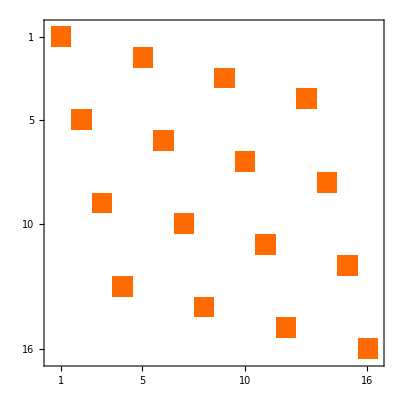

```mathematica
T =permutationMatrix[{3,4,1,2}];
MatrixPlot[T]
```

```mathematica
permdouble=Permutations@{{1,2},{3,4},{5,6},{7,8}}
```

{{{1,2},{3,4},{5,6},{7,8}},{{1,2},{3,4},{7,8},{5,6}},{{1,2},{5,6},{3,4},{7,8}},{{1,2},{5,6},{7,8},{3,4}},{{1,2},{7,8},{3,4},{5,6}},{{1,2},{7,8},{5,6},{3,4}},{{3,4},{1,2},{5,6},{7,8}},{{3,4},{1,2},{7,8},{5,6}},{{3,4},{5,6},{1,2},{7,8}},{{3,4},{5,6},{7,8},{1,2}},{{3,4},{7,8},{1,2},{5,6}},{{3,4},{7,8},{5,6},{1,2}},{{5,6},{1,2},{3,4},{7,8}},{{5,6},{1,2},{7,8},{3,4}},{{5,6},{3,4},{1,2},{7,8}},{{5,6},{3,4},{7,8},{1,2}},{{5,6},{7,8},{1,2},{3,4}},{{5,6},{7,8},{3,4},{1,2}},{{7,8},{1,2},{3,4},{5,6}},{{7,8},{1,2},{5,6},{3,4}},{{7,8},{3,4},{1,2},{5,6}},{{7,8},{3,4},{5,6},{1,2}},{{7,8},{5,6},{1,2},{3,4}},{{7,8},{5,6},{3,4},{1,2}}}

Compute the application of the computed commutator and the Permutation Matrix

```mathematica
oo=(1/16)*(1/24)*Sum[pp.permutationMatrix[Flatten[permdouble[[i]]]],{i,1,24}]
```

{1}
 |  |  |  |

```mathematica
MatrixPlot[oo,PlotTheme->"Detailed"]
```

-Graphics-

```mathematica
Sum[oo[[i,j]]^2,{i,1,256},{j,1,256}]
```

6

```mathematica
Tr[ConjugateTranspose[oo].oo]
```

6

```mathematica
3./7.
```

0.428571

```mathematica
3./10.
```

0.3

# Testing around

```mathematica
H = 1/Sqrt[2]*({{1, 1}, {1, -1}});
iden=({{1, 0}, {0, 1}});
X=({{0, 1}, {1, 0}});
Y=({{0, -I}, {I, 0}});
Z=({{1, 0}, {0, -1}});
S=({{1, 0}, {0, E^(I*Pi/2)}});

T=({{1, 0}, {0, E^(I*Pi/4)}});

zerozero = ({{1, 0}, {0, 0}});
oneone = ({{0, 0}, {0, 1}});
SWAP=({{1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}});
u1N2=KroneckerProduct[H,iden];
u2N2=KroneckerProduct[zerozero,iden]+KroneckerProduct[oneone,S];
u3N2=KroneckerProduct[iden,H];
FTN2=SWAP.u3N2.u2N2.u1N2;

u1N3=KroneckerProduct[H,iden,iden];
u2N3=KroneckerProduct[oneone,S,iden]+KroneckerProduct[zerozero,iden,iden];
u3N3=KroneckerProduct[oneone,iden,T]+KroneckerProduct[zerozero,iden,iden];
u4N3=KroneckerProduct[iden,H,iden];
u5N3=KroneckerProduct[iden,oneone,S]+KroneckerProduct[iden,zerozero,iden];
u6N3=KroneckerProduct[iden,iden,H];
u7N3=(KroneckerProduct[iden,iden,iden]+KroneckerProduct[X,iden,X]+KroneckerProduct[Y,iden,Y]+KroneckerProduct[Z,iden,Z])/2;
FTN3=u7N3.u6N3.u5N3.u4N3.u3N3.u2N3.u1N3;
(*https://arxiv.org/pdf/quant-ph/0201067*)
```

```mathematica
u7N3//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

# N=2

```mathematica
2*FTN2//MatrixForm
```

(1 | 1 | 1 | 1
1 | ⅈ | -1 | -ⅈ
1 | -1 | 1 | -1
1 | -ⅈ | -1 | ⅈ)

```mathematica
2*FTN2.({{1}, {0}, {1}, {1}})//MatrixForm
```

(3
-ⅈ
1
ⅈ)

```mathematica
2*FourierMatrix[4].({{1}, {0}, {1}, {1}})//MatrixForm
```

(3
-ⅈ
1
ⅈ)

# N=3

```mathematica
Sqrt[8]*FTN3//MatrixForm//N
```

(1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 0.707107+0.707107 ⅈ | 0.+1. ⅈ | -0.707107+0.707107 ⅈ | -1. | -0.707107-0.707107 ⅈ | 0.-1. ⅈ | 0.707107-0.707107 ⅈ
1. | 0.+1. ⅈ | -1. | 0.-1. ⅈ | 1. | 0.+1. ⅈ | -1. | 0.-1. ⅈ
1. | -0.707107+0.707107 ⅈ | 0.-1. ⅈ | 0.707107+0.707107 ⅈ | -1. | 0.707107-0.707107 ⅈ | 0.+1. ⅈ | -0.707107-0.707107 ⅈ
1. | -1. | 1. | -1. | 1. | -1. | 1. | -1.
1. | -0.707107-0.707107 ⅈ | 0.+1. ⅈ | 0.707107-0.707107 ⅈ | -1. | 0.707107+0.707107 ⅈ | 0.-1. ⅈ | -0.707107+0.707107 ⅈ
1. | 0.-1. ⅈ | -1. | 0.+1. ⅈ | 1. | 0.-1. ⅈ | -1. | 0.+1. ⅈ
1. | 0.707107-0.707107 ⅈ | 0.-1. ⅈ | -0.707107-0.707107 ⅈ | -1. | -0.707107+0.707107 ⅈ | 0.+1. ⅈ | 0.707107+0.707107 ⅈ)

```mathematica
n=8;(*Size of the matrix*)
DFTMatrix=FourierMatrix[n];(*Generating DFT matrix*)
MatrixForm[Sqrt[8]*DFTMatrix]//N (*Displaying the matrix*)
```

(1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1. | 0.707107+0.707107 ⅈ | 0.+1. ⅈ | -0.707107+0.707107 ⅈ | -1. | -0.707107-0.707107 ⅈ | 0.-1. ⅈ | 0.707107-0.707107 ⅈ
1. | 0.+1. ⅈ | -1. | 0.-1. ⅈ | 1. | 0.+1. ⅈ | -1. | 0.-1. ⅈ
1. | -0.707107+0.707107 ⅈ | 0.-1. ⅈ | 0.707107+0.707107 ⅈ | -1. | 0.707107-0.707107 ⅈ | 0.+1. ⅈ | -0.707107-0.707107 ⅈ
1. | -1. | 1. | -1. | 1. | -1. | 1. | -1.
1. | -0.707107-0.707107 ⅈ | 0.+1. ⅈ | 0.707107-0.707107 ⅈ | -1. | 0.707107+0.707107 ⅈ | 0.-1. ⅈ | -0.707107+0.707107 ⅈ
1. | 0.-1. ⅈ | -1. | 0.+1. ⅈ | 1. | 0.-1. ⅈ | -1. | 0.+1. ⅈ
1. | 0.707107-0.707107 ⅈ | 0.-1. ⅈ | -0.707107-0.707107 ⅈ | -1. | -0.707107+0.707107 ⅈ | 0.+1. ⅈ | 0.707107+0.707107 ⅈ)

```mathematica
FTN3.({{1}, {1}, {0}, {0}, {0}, {0}, {0}, {0}})//MatrixForm//N
```

(0.707107
0.603553+0.25 ⅈ
0.353553+0.353553 ⅈ
0.103553+0.25 ⅈ
0.
0.103553-0.25 ⅈ
0.353553-0.353553 ⅈ
0.603553-0.25 ⅈ)

```mathematica
Sqrt[8]*DFTMatrix.({{1}, {0}, {0}, {1}, {0}, {0}, {1}, {0}})//MatrixForm//N
```

(3.
0.292893-0.292893 ⅈ
0.-1. ⅈ
1.70711+1.70711 ⅈ
1.
1.70711-1.70711 ⅈ
0.+1. ⅈ
0.292893+0.292893 ⅈ)

Seems that DFTMatrix is doing the fourier transform as it is given in the wikipedia page

# Numerical N =2

```mathematica
H = 1/Sqrt[2]*({{1, 1}, {1, -1}});
iden=({{1, 0}, {0, 1}});
X=({{0, 1}, {1, 0}});
Y=({{0, -I}, {I, 0}});
Z=({{1, 0}, {0, -1}});
S=({{1, 0}, {0, E^(I*Pi/2)}});

zerozero = ({{1, 0}, {0, 0}});
oneone = ({{0, 0}, {0, 1}});
u2=FourierMatrix[4];
parser[p_]:=Which[p===0,iden,p===1,X,p===2,Y,p===3,Z];
PauliString[i_,j_]:=KroneckerProduct[parser[i],parser[j]];
pp=Sum[KroneckerProduct[u2,u2,u2,u2].KroneckerProduct[PauliString[i,j],PauliString[i,j],PauliString[i,j],PauliString[i,j]] -KroneckerProduct[PauliString[i,j],PauliString[i,j],PauliString[i,j],PauliString[i,j]].KroneckerProduct[u2,u2,u2,u2] ,{i,0,3},{j,0,3}]
```

{1}
 |  |  |  |

```mathematica
Sqrt[Tr[ConjugateTranspose[pp].pp]]
```

48 √2

```mathematica
MatrixPlot[pp,PlotTheme->"Detailed"]
```

-Graphics-

```mathematica
permdouble=Permutations@{{1,2},{3,4},{5,6},{7,8}}
```

{{{1,2},{3,4},{5,6},{7,8}},{{1,2},{3,4},{7,8},{5,6}},{{1,2},{5,6},{3,4},{7,8}},{{1,2},{5,6},{7,8},{3,4}},{{1,2},{7,8},{3,4},{5,6}},{{1,2},{7,8},{5,6},{3,4}},{{3,4},{1,2},{5,6},{7,8}},{{3,4},{1,2},{7,8},{5,6}},{{3,4},{5,6},{1,2},{7,8}},{{3,4},{5,6},{7,8},{1,2}},{{3,4},{7,8},{1,2},{5,6}},{{3,4},{7,8},{5,6},{1,2}},{{5,6},{1,2},{3,4},{7,8}},{{5,6},{1,2},{7,8},{3,4}},{{5,6},{3,4},{1,2},{7,8}},{{5,6},{3,4},{7,8},{1,2}},{{5,6},{7,8},{1,2},{3,4}},{{5,6},{7,8},{3,4},{1,2}},{{7,8},{1,2},{3,4},{5,6}},{{7,8},{1,2},{5,6},{3,4}},{{7,8},{3,4},{1,2},{5,6}},{{7,8},{3,4},{5,6},{1,2}},{{7,8},{5,6},{1,2},{3,4}},{{7,8},{5,6},{3,4},{1,2}}}

```mathematica
oo=(1/16)*(1/24)*Sum[pp.permutationMatrix[Flatten[permdouble[[i]]]],{i,1,24}]
```

{1}
 |  |  |  |

```mathematica
MatrixPlot[oo,PlotTheme->"Detailed"]
```

-Graphics-

```mathematica
Tr[ConjugateTranspose[oo].oo]
```

6

```mathematica
18*4/(5*6*8)
```

3/10

```mathematica
0.6965823615936906
```

```mathematica
Sqrt[2]/2//N
```

0.707107

```mathematica
0.69658236159/2
```

0.348291

# CONTROL+T

```mathematica
H = 1/Sqrt[2]*({{1, 1}, {1, -1}});
iden=({{1, 0}, {0, 1}});
X=({{0, 1}, {1, 0}});
Y=({{0, -I}, {I, 0}});
Z=({{1, 0}, {0, -1}});
S=({{1, 0}, {0, E^(I*Pi/2)}});
T=({{1, 0}, {0, E^(I*Pi/4)}});

zerozero = ({{1, 0}, {0, 0}});
oneone = ({{0, 0}, {0, 1}});
u2=KroneckerProduct[zerozero,T]+KroneckerProduct[oneone,iden];
parser[p_]:=Which[p===0,iden,p===1,X,p===2,Y,p===3,Z];
PauliString[i_,j_]:=KroneckerProduct[parser[i],parser[j]];
pp=Sum[KroneckerProduct[u2,u2,u2,u2].KroneckerProduct[PauliString[i,j],PauliString[i,j],PauliString[i,j],PauliString[i,j]] -KroneckerProduct[PauliString[i,j],PauliString[i,j],PauliString[i,j],PauliString[i,j]].KroneckerProduct[u2,u2,u2,u2] ,{i,0,3},{j,0,3}]
```

{1}
 |  |  |  |

```mathematica
Sqrt[Tr[ConjugateTranspose[pp].pp]]
```

8 √42

```mathematica
MatrixPlot[pp,PlotTheme->"Detailed"]
```

-Graphics-

```mathematica
permdouble=Permutations@{{1,2},{3,4},{5,6},{7,8}}
```

{{{1,2},{3,4},{5,6},{7,8}},{{1,2},{3,4},{7,8},{5,6}},{{1,2},{5,6},{3,4},{7,8}},{{1,2},{5,6},{7,8},{3,4}},{{1,2},{7,8},{3,4},{5,6}},{{1,2},{7,8},{5,6},{3,4}},{{3,4},{1,2},{5,6},{7,8}},{{3,4},{1,2},{7,8},{5,6}},{{3,4},{5,6},{1,2},{7,8}},{{3,4},{5,6},{7,8},{1,2}},{{3,4},{7,8},{1,2},{5,6}},{{3,4},{7,8},{5,6},{1,2}},{{5,6},{1,2},{3,4},{7,8}},{{5,6},{1,2},{7,8},{3,4}},{{5,6},{3,4},{1,2},{7,8}},{{5,6},{3,4},{7,8},{1,2}},{{5,6},{7,8},{1,2},{3,4}},{{5,6},{7,8},{3,4},{1,2}},{{7,8},{1,2},{3,4},{5,6}},{{7,8},{1,2},{5,6},{3,4}},{{7,8},{3,4},{1,2},{5,6}},{{7,8},{3,4},{5,6},{1,2}},{{7,8},{5,6},{1,2},{3,4}},{{7,8},{5,6},{3,4},{1,2}}}

```mathematica
oo=(1/16)*(1/24)*Sum[pp.permutationMatrix[Flatten[permdouble[[i]]]],{i,1,24}]
```

{1}
 |  |  |  |

```mathematica
MatrixPlot[oo,PlotTheme->"Detailed"]
```

-Graphics-

```mathematica
Tr[ConjugateTranspose[oo].oo]
```

9/2

# Control + T1

```mathematica
H = 1/Sqrt[2]*({{1, 1}, {1, -1}});
iden=({{1, 0}, {0, 1}});
X=({{0, 1}, {1, 0}});
Y=({{0, -I}, {I, 0}});
Z=({{1, 0}, {0, -1}});
S=({{1, 0}, {0, E^(I*Pi/2)}});
T=({{1, 0}, {0, E^(I*Pi/4)}});
T1=({{1, 0}, {0, E^(I*Pi/16)}});

zerozero = ({{1, 0}, {0, 0}});
oneone = ({{0, 0}, {0, 1}});
u2=KroneckerProduct[zerozero,T1]+KroneckerProduct[oneone,iden];
parser[p_]:=Which[p===0,iden,p===1,X,p===2,Y,p===3,Z];
PauliString[i_,j_]:=KroneckerProduct[parser[i],parser[j]];
pp=Sum[KroneckerProduct[u2,u2,u2,u2].KroneckerProduct[PauliString[i,j],PauliString[i,j],PauliString[i,j],PauliString[i,j]] -KroneckerProduct[PauliString[i,j],PauliString[i,j],PauliString[i,j],PauliString[i,j]].KroneckerProduct[u2,u2,u2,u2] ,{i,0,3},{j,0,3}]
```

{1}
 |  |  |  |

```mathematica
Sqrt[Tr[ConjugateTranspose[pp].pp]]//N
```

15.219-2.3344×10^-16 ⅈ

```mathematica
MatrixPlot[pp,PlotTheme->"Detailed"]
```

-Graphics-

```mathematica
permdouble=Permutations@{{1,2},{3,4},{5,6},{7,8}}
```

{{{1,2},{3,4},{5,6},{7,8}},{{1,2},{3,4},{7,8},{5,6}},{{1,2},{5,6},{3,4},{7,8}},{{1,2},{5,6},{7,8},{3,4}},{{1,2},{7,8},{3,4},{5,6}},{{1,2},{7,8},{5,6},{3,4}},{{3,4},{1,2},{5,6},{7,8}},{{3,4},{1,2},{7,8},{5,6}},{{3,4},{5,6},{1,2},{7,8}},{{3,4},{5,6},{7,8},{1,2}},{{3,4},{7,8},{1,2},{5,6}},{{3,4},{7,8},{5,6},{1,2}},{{5,6},{1,2},{3,4},{7,8}},{{5,6},{1,2},{7,8},{3,4}},{{5,6},{3,4},{1,2},{7,8}},{{5,6},{3,4},{7,8},{1,2}},{{5,6},{7,8},{1,2},{3,4}},{{5,6},{7,8},{3,4},{1,2}},{{7,8},{1,2},{3,4},{5,6}},{{7,8},{1,2},{5,6},{3,4}},{{7,8},{3,4},{1,2},{5,6}},{{7,8},{3,4},{5,6},{1,2}},{{7,8},{5,6},{1,2},{3,4}},{{7,8},{5,6},{3,4},{1,2}}}

```mathematica
oo=(1/16)*(1/24)*Sum[pp.permutationMatrix[Flatten[permdouble[[i]]]],{i,1,24}]
```

{1}
 |  |  |  |

```mathematica
MatrixPlot[oo,PlotTheme->"Detailed"]
```

-Graphics-

```mathematica
Tr[ConjugateTranspose[oo].oo]//N
```

0.448031+6.93889×10^-18 ⅈ

# Numerical N = 3

```mathematica
H = 1/Sqrt[2]*({{1, 1}, {1, -1}});
iden=({{1, 0}, {0, 1}});
X=({{0, 1}, {1, 0}});
Y=({{0, -I}, {I, 0}});
Z=({{1, 0}, {0, -1}});
S=({{1, 0}, {0, E^(I*Pi/2)}});

zerozero = ({{1, 0}, {0, 0}});
oneone = ({{0, 0}, {0, 1}});
u3=FourierMatrix[8];
U=SparseArray[KroneckerProduct[u3,u3,u3,u3]]
```

SparseArray[<16777216>, {4096, 4096}]

```mathematica
parser[p_]:=Which[p===0,iden,p===1,X,p===2,Y,p===3,Z];
PauliString[i_,j_,k_]:=KroneckerProduct[parser[i],parser[j],parser[k]];
PPP=SparseArray[Sum[KroneckerProduct[PauliString[i,j,k],PauliString[i,j,k],PauliString[i,j,k],PauliString[i,j,k]],{i,0,3},{j,0,3},{k,0,3}]]
```

SparseArray[…]

```mathematica
pp=U.PPP-PPP.U
```

SparseArray[<3932160>, {4096, 4096}]

```mathematica
permtriple=Permutations@{{1,2,3},{4,5,6},{7,8,9},{10,11,12}};
```

{{{1,2,3},{4,5,6},{7,8,9},{10,11,12}},{{1,2,3},{4,5,6},{10,11,12},{7,8,9}},{{1,2,3},{7,8,9},{4,5,6},{10,11,12}},{{1,2,3},{7,8,9},{10,11,12},{4,5,6}},{{1,2,3},{10,11,12},{4,5,6},{7,8,9}},{{1,2,3},{10,11,12},{7,8,9},{4,5,6}},{{4,5,6},{1,2,3},{7,8,9},{10,11,12}},{{4,5,6},{1,2,3},{10,11,12},{7,8,9}},{{4,5,6},{7,8,9},{1,2,3},{10,11,12}},{{4,5,6},{7,8,9},{10,11,12},{1,2,3}},{{4,5,6},{10,11,12},{1,2,3},{7,8,9}},{{4,5,6},{10,11,12},{7,8,9},{1,2,3}},{{7,8,9},{1,2,3},{4,5,6},{10,11,12}},{{7,8,9},{1,2,3},{10,11,12},{4,5,6}},{{7,8,9},{4,5,6},{1,2,3},{10,11,12}},{{7,8,9},{4,5,6},{10,11,12},{1,2,3}},{{7,8,9},{10,11,12},{1,2,3},{4,5,6}},{{7,8,9},{10,11,12},{4,5,6},{1,2,3}},{{10,11,12},{1,2,3},{4,5,6},{7,8,9}},{{10,11,12},{1,2,3},{7,8,9},{4,5,6}},{{10,11,12},{4,5,6},{1,2,3},{7,8,9}},{{10,11,12},{4,5,6},{7,8,9},{1,2,3}},{{10,11,12},{7,8,9},{1,2,3},{4,5,6}},{{10,11,12},{7,8,9},{4,5,6},{1,2,3}}}

```mathematica
oo=(1/64)*(1/24)*Sum[SparseArray[permutationMatrix[Flatten[permtriple[[i]]]]],{i,1,24}];
oo=pp.oo;
```

Part::partd: Part specification permdouble⟦1⟧ is longer than depth of object.

Dot::dotsh: Tensors SparseArray[Automatic,«2»,{1,{{0,4096,«4093»,3928064,3932160},{«1»}},{0,1,0,1,0,1,0,1,1,1,1,1,1,1,1,1,1,0,1,0,1,0,1,0,1,1,1,1,1,1,1,1,0,1,0,1,0,1,0,1,1,1,1,1,1,1,1,1,1,0,«3932110»}}] and SparseArray[Automatic,{4,4},0,{1,{{0,0,0,0,0},{}},{}}] have incompatible shapes.

Part::partd: Part specification permdouble⟦2⟧ is longer than depth of object.

Dot::dotsh: Tensors SparseArray[Automatic,«2»,{1,{{0,4096,«4093»,3928064,3932160},{«1»}},{0,1,0,1,0,1,0,1,1,1,1,1,1,1,1,1,1,0,1,0,1,0,1,0,1,1,1,1,1,1,1,1,0,1,0,1,0,1,0,1,1,1,1,1,1,1,1,1,1,0,«3932110»}}] and SparseArray[Automatic,{4,4},0,{1,{{0,0,0,0,0},{}},{}}] have incompatible shapes.

Part::partd: Part specification permdouble⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Dot::dotsh: Tensors SparseArray[Automatic,«2»,{1,{{0,4096,«4093»,3928064,3932160},{«1»}},{0,1,0,1,0,1,0,1,1,1,1,1,1,1,1,1,1,0,1,0,1,0,1,0,1,1,1,1,1,1,1,1,0,1,0,1,0,1,0,1,1,1,1,1,1,1,1,1,1,0,«3932110»}}] and SparseArray[Automatic,{4,4},0,{1,{{0,0,0,0,0},{}},{}}] have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

1/64 SparseArray[<3932160>, {4096, 4096}].SparseArray[…]

```mathematica
f[L_]:=(3*2^L)/((2^L+1)*(2^L+2)*(2^L+4))*33/2
```

```mathematica
f[3]//N
```

0.366667

```mathematica
lista={{1,6},{2,4.5},{3,1.62},{4,0.449}}
```

```mathematica
{{1,6},{2,4.5},{3,1.62},{4,0.448}}
```

{{1,6},{2,4.5},{3,1.62},{4,0.448}}

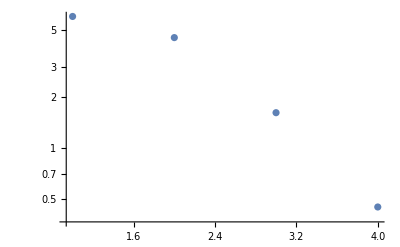

```mathematica
ListLogPlot[lista]
```

```mathematica
R[k_]:=({{1, 0}, {0, E^((2*Pi*I)/2^k)}});
```

```mathematica
R[3].PauliMatrix[1]-PauliMatrix[1].R[3]//MatrixForm
```

(0 | 1-ⅇ^((ⅈ π)/4)
-1+ⅇ^((ⅈ π)/4) | 0)

```mathematica
I*(1-E^((2*Pi*I)/2^3))*PauliMatrix[2]//MatrixForm
```

(0 | 1-ⅇ^((ⅈ π)/4)
-1+ⅇ^((ⅈ π)/4) | 0)

```mathematica
R[4].PauliMatrix[1]-PauliMatrix[1].R[4]//MatrixForm
```

(0 | 1-ⅇ^((ⅈ π)/8)
-1+ⅇ^((ⅈ π)/8) | 0)

```mathematica
I*(1-E^((2*Pi*I)/2^4))*PauliMatrix[2]//MatrixForm
```

(0 | 1-ⅇ^((ⅈ π)/8)
-1+ⅇ^((ⅈ π)/8) | 0)

```mathematica
R[5].PauliMatrix[1]-PauliMatrix[1].R[5]//MatrixForm
```

(0 | 1-ⅇ^((ⅈ π)/16)
-1+ⅇ^((ⅈ π)/16) | 0)

```mathematica
I*(1-E^((2*Pi*I)/2^5))*PauliMatrix[2]//MatrixForm
```

(0 | 1-ⅇ^((ⅈ π)/16)
-1+ⅇ^((ⅈ π)/16) | 0)

```mathematica
R[5].PauliMatrix[1]-PauliMatrix[1].R[5]//MatrixForm
```

```mathematica
R[4].PauliMatrix[0]+PauliMatrix[0].R[4]//MatrixForm
```

(2 | 0
0 | 2 ⅇ^((ⅈ π)/8))

```mathematica
1.2429197548353321-0.9548153083608708
```

0.288104

```mathematica
MlinBOUND[L_]:=1-1/(4+2^L)*(4+(2^L+3)/4*2^(-L*Log[L]));
MlinBOUNDSQUARE[L_]:=1-1/(4+2^L)*(4+(2^L+3)/4*2^(-L*Log[L]*Log[L]));
```

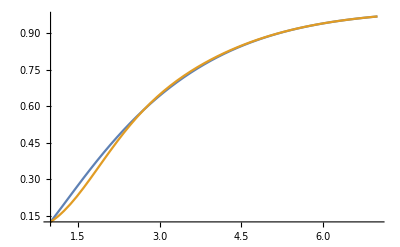

```mathematica
Plot[{MlinBOUND[L],MlinBOUNDSQUARE[L]},{L,1,7}]
```

```mathematica
MlinBOUND[2]//N
```

0.416318

```mathematica
MlinBOUND[L]//FullSimplify
```

1-(4+2^(-2-L Log[L]) (3+2^L))/(4+2^L)

```mathematica
-Log[1-MlinBOUND[L]]//FullSimplify
```

-Log[(4+2^(-2-L Log[L]) (3+2^L))/(4+2^L)]

```mathematica
Series[-Log[1-MlinBOUND[L]],{L,Infinity,0}]
```

-Log[4/(4+ⅇ^(Log[2] L+O[1/L]^2))+(3 ⅇ^(-Log[2] Log[L] L-2 Log[2]+O[1/L]^2))/(4+ⅇ^(Log[2] L+O[1/L]^2))+(ⅇ^((Log[2]-Log[2] Log[L]) L-2 Log[2]+O[1/L]^2))/(4+ⅇ^(Log[2] L+O[1/L]^2))]

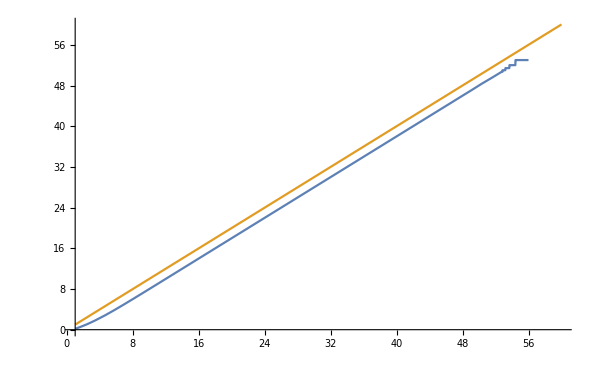

```mathematica
Plot[{-Log[2,1-MlinBOUND[L]],L*Log[2,2]},{L,1,60}]
```

```mathematica
Log[E^(Log[2]*L)]
```

Log[2^L]

```mathematica
Log[2]//N
```

0.693147

```mathematica
f[L_]:=Log[2^L+1]-Log[2];
fres[L_]:=Log[2]*L;
```

```mathematica
f[10]//N
```

6.2393

```mathematica
fres[10]//N
```

6.93147

```mathematica
mlinHaar[L_]:=1-4/(2^L+3);
MlinBOUND[L_]:=1-1/(4+2^L)*(4+(2^L+3)/4*2^(-L*Log[L]));
```

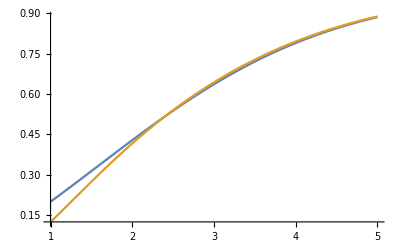

```mathematica
Plot[{mlinHaar[L],MlinBOUND[L]},{L,1,5}]
```

```mathematica
mlinHaar[20]//N
```

0.999996

```mathematica
NumberForm[0.9999961853136483,16]
```

0.999996185313648

```mathematica
MlinBOUND[20]//N
```

0.999996

```mathematica
NumberForm[0.9999961853172862,16]
```

0.999996185317286

```mathematica
Log[2]//N
```

0.693147

```mathematica
Tr[FourierMatrix[16].FourierMatrix[16]]//N
```

2.+0. ⅈ

```mathematica
MlinBOUND[L_]:=1-1/(4+2^L)*(4+(2^L+3)/4*2^(-L*Log[L]));
```

```mathematica
Series[MlinBOUND[L],{L,Infinity,0}]//FullSimplify
```

(ⅇ^(Log[2] L+O[1/L]^2)-3 ⅇ^(-Log[2] Log[L] L-Log[4]+O[1/L]^2)-ⅇ^((Log[2]-Log[2] Log[L]) L-Log[4]+O[1/L]^2))/(4+ⅇ^(Log[2] L+O[1/L]^2))

```mathematica
E^(Log[2]*L)
```

2^L

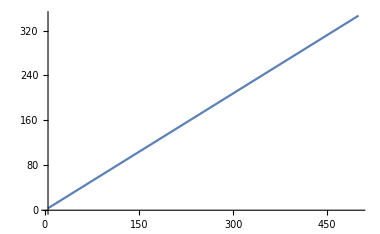

```mathematica
Plot[L*Log[2],{L,5,500}]
```

```mathematica
Series[1/(4+2^L)*(4+(2^L+3)/4*2^(-L*Log[L])),{L,Infinity,0}]
```

4/(4+ⅇ^(Log[2] L+O[1/L]^2))+(3 ⅇ^(-Log[2] Log[L] L-2 Log[2]+O[1/L]^2))/(4+ⅇ^(Log[2] L+O[1/L]^2))+(ⅇ^((Log[2]-Log[2] Log[L]) L-2 Log[2]+O[1/L]^2))/(4+ⅇ^(Log[2] L+O[1/L]^2))

```mathematica
E^(Log[2]*L)
```

2^L

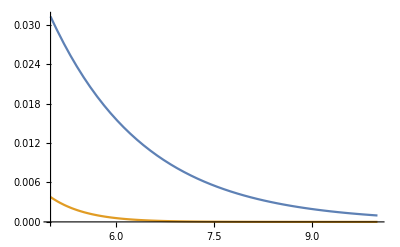

```mathematica
Plot[{2^-L,2^(-L*Log[L])},{L,5,10}]
```

```mathematica
-Log[3/4]//N
```

0.287682

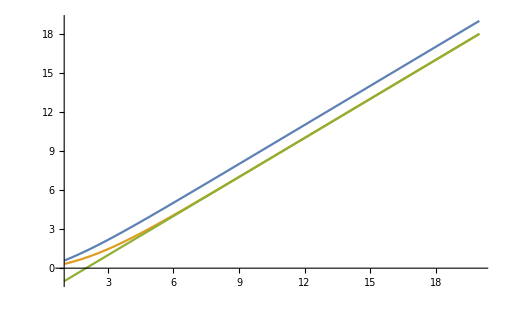

```mathematica
Plot[{Log[2,2^L+1]-Log[2,2],(Log[2,2^L+3]-2*Log[2,2]),Log[2,2^L]-2*Log[2,2]},{L,1,20}]
```

```mathematica
Series[Log[2,2^L+3]-2*Log[2,2],{L,Infinity,0}]
```

-2+Log[3+ⅇ^(Log[2] L+O[1/L]^2)]/Log[2]

```mathematica
-0.6745649769717169/14
```

-0.0481832

```mathematica
-0.592409230760932/12
```

-0.0493674

```mathematica
-Log[2.0]
```

-0.693147

```mathematica
2^7
```

128

```mathematica
f[L_,epsi_]:=L*Log[L/epsi]+Log[L/epsi]*Log[Log[L/epsi]/epsi]
```

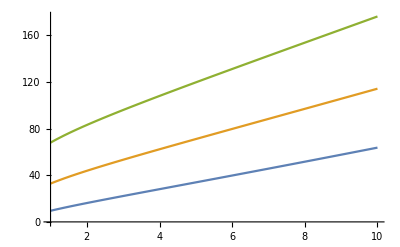

```mathematica
Plot[{f[L,0.1],f[L,0.01],f[L,0.001]},{L,1,10}]
```

```mathematica
Series[f[L,epsi],{epsi,0,2}]
```

(L Log[L/epsi]+Log[L/epsi] Log[Log[L/epsi]/epsi])+O[epsi]^3

```mathematica
Limit[f[L,epsi],L->Infinity]
```

∞